```mathematica
fitO:=o+(1/2*y)+(a*B);
fitY:=(2*o)+y+(s*B);
fitB:=(o*1/2)+(2*y)+B;

fitmedio:=fitO*o+fitY*y+fitB*B;

dodt:=o*(fitO-fitmedio);
dydt:=y*(fitY-fitmedio);
dbdt:=B*(fitB-fitmedio);

equilibrio = Solve[{dodt == 0 && dydt == 0 && dbdt == 0, o + y + B ==1}, {o, y, B}]
jacobiana=FullSimplify[D[{dodt,dydt,dbdt},{{o,y,B}}]];
```

{{o→-1,y→2,B→0},{o→0,y→1,B→0},{o→1,y→0,B→0},{o→0,y→0,B→1},{o→(2 (-1+a))/(-3+2 a),y→0,B→1/(3-2 a)},{o→(2 (1+2 a-3 s))/(5+10 a-8 s),y→(2 (-2+3 a-s))/(5+10 a-8 s),B→7/(5+10 a-8 s)},{o→0,y→(-1+s)/s,B→1/s}}

```mathematica
mat1=jacobiana/. equilibrio[[1]];
autovalores1=Eigenvalues[mat1];
Resolve[Exists[{a, s},o + y + B ==1 && 0<= o <=1 && 0<= B <=1 &&0<= y <=1 && Max[Re[autovalores1]]<0]]

(*sol = NDSolve[{o'[t]==dodt,y'[t]==dydt,B'[t]==dbdt,o[0]==0.4,y[0]==0.15,B[0]==0.45},{o,y,B},{t,0,200}];
Plot[{o[t]/. sol[[1]],y[t]/. sol[[1]],B[t]/. sol[[1]]},{t,0,200},PlotLegends->{"o","y","B"}]*)
```

False

```mathematica
mat2=jacobiana/. equilibrio[[2]];
autovalores2=Eigenvalues[mat2];
Resolve[Exists[{a, s},o + y + B ==1 && 0<= o <=1 && 0<= B <=1 &&0<= y <=1 && Max[Re[autovalores2]]<0]]
```

False

```mathematica
equilibrio[[5]]
mat5=jacobiana/. equilibrio[[5]];
autovalores5=Eigenvalues[mat5];
Resolve[Exists[{a, s},o + y + B ==1 && 0<= (2 (-1+a))/(-3+2 a)<=1 && 0<=1/(3-2 a) <=1 && Max[Re[autovalores5]]<0]]
```

{o→(2 (-1+a))/(-3+2 a),y→0,B→1/(3-2 a)}

False

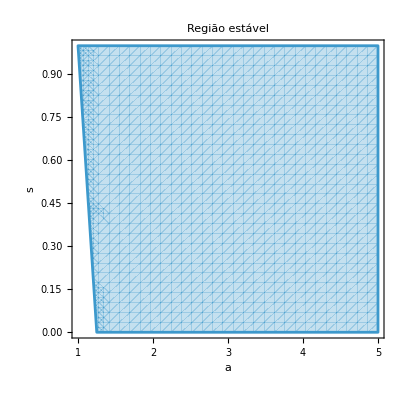

```mathematica
RegionPlot[Max[Re[Eigenvalues[mat6/. {a->A,s->S}]//N]]<0,{A,1,5},{S,0,1},PlotPoints->30,FrameLabel->{"a","s"},PlotLabel->"Região estável"]
```

```mathematica
equilibrio[[6]]
mat6=jacobiana/. equilibrio[[6]];
autovalores6=Eigenvalues[mat6];
Resolve[Exists[{a, s},o + y + B ==1 && a >= s && a>=0 && s >=0 &&  0<= (2 (1+2 a-3 s))/(5+10 a-8 s)<=1 && 0<=(2 (-2+3 a-s))/(5+10 a-8 s)<=1 &&0<= 7/(5+10 a-8 s) <=1&& Max[Re[autovalores6]]<0]]
```

{o→(2 (1+2 a-3 s))/(5+10 a-8 s),y→(2 (-2+3 a-s))/(5+10 a-8 s),B→7/(5+10 a-8 s)}

Max[-7 Re[(10 a+20 a^2-5 s-26 a s+8 s^2)/(5+10 a-8 s)^2],1/2 Re[1/(5+10 a-8 s)^2(25+30 a-40 a^2-45 s+22 a s+8 s^2-√(2025+7800 a+3100 a^2-16400 a^3-15200 a^4-10230 s-19100 a s+30680 a^2 s+55920 a^3 s+15109 s^2-10348 a s^2-68588 a^2 s^2-2960 s^3+33504 a s^3-5312 s^4))],1/2 Re[1/(5+10 a-8 s)^2(25+30 a-40 a^2-45 s+22 a s+8 s^2+√(2025+7800 a+3100 a^2-16400 a^3-15200 a^4-10230 s-19100 a s+30680 a^2 s+55920 a^3 s+15109 s^2-10348 a s^2-68588 a^2 s^2-2960 s^3+33504 a s^3-5312 s^4))]]

y==1-B-o

```mathematica
equilibrio[[7]]
mat7=jacobiana/. equilibrio[[7]];
autovalores7=Eigenvalues[mat7];
Resolve[Exists[{a, s},o + y + B ==1 && a >= s && a>=0 && s >=0 && 0<= (-1+s)/s<=1 && 0<=1/s<=1 && Max[Re[autovalores7]]<0]]
```

{o→0,y→(-1+s)/s,B→1/s}

Im[B]+Im[o]+Im[y]==0&&-1+Re[B]+Re[o]+Re[y]==0

{{o→InterpolatingFunction[…],y→InterpolatingFunction[…],B→InterpolatingFunction[…]}}

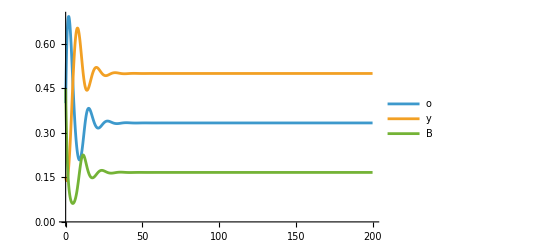

```mathematica
fitO=o[t]+0.5*y[t]+4.5*B[t];
fitY=2*o[t]+y[t]+0.9999*B[t];
fitB=o[t]*0.5+2*y[t]+B[t];

fitmedio=fitO*o[t]+fitY*y[t]+fitB*B[t];

dodt=o[t]*(fitO-fitmedio);
dydt=y[t]*(fitY-fitmedio);
dbdt=B[t]*(fitB-fitmedio);

sol = NDSolve[{o'[t]==dodt,y'[t]==dydt,B'[t]==dbdt,o[0]==0.4,y[0]==0.15,B[0]==0.45},{o,y,B},{t,0,200}]
Plot[{o[t]/. sol[[1]],y[t]/. sol[[1]],B[t]/. sol[[1]]},{t,0,200},PlotLegends->{"o","y","B"}]
```